Vspec = 14.0446   Pspec=abc = 3.3529

N = 600   λ1 = 5.30468   λN = 207.869

Fw min/max: {-5.11377,3.93388}

S(L) min/max: {0.187171,34298.2}

#topPeaks = 14

Top 12 peaks (L,S):

11.281 | 34298.2
13.9277 | 27410.7
22.1 | 15327.8
7.57627 | 8448.18
33.506 | 6046.32
24.7666 | 4682.74
38.9055 | 2977.37
26.0833 | 2920.73
27.9738 | 1226.17
29.9571 | 735.376
36.3019 | 549.761
4.0009 | 239.719

#axes candidates = 227

#near candidates within radius 0.5 = 69

Top 30 nearest candidates (a,b,c):

0.957683 | 1.51962 | 2.30391
0.897693 | 1.5963 | 2.3398
0.932436 | 1.47956 | 2.43036
0.994097 | 1.5774 | 2.13821
0.921999 | 1.63952 | 2.21806
0.882326 | 1.65239 | 2.29974
1.07347 | 1.32532 | 2.35672
0.877204 | 1.55987 | 2.45038
1.11502 | 1.37662 | 2.18437
0.862188 | 1.61467 | 2.40843
0.856337 | 1.62159 | 2.41454
0.863789 | 1.6922 | 2.29383
1.05509 | 1.30264 | 2.43953
0.906215 | 1.69713 | 2.18009
0.855107 | 1.57197 | 2.49434
0.84231 | 1.69178 | 2.3529
0.911154 | 1.44579 | 2.54521
0.832148 | 1.63021 | 2.47158
0.861984 | 1.7313 | 2.24673
0.883739 | 1.73128 | 2.19143
1.01706 | 1.61383 | 2.04276
1.17294 | 1.38435 | 2.06489
0.957056 | 1.70186 | 2.05854
1.19337 | 1.33736 | 2.10085
1.1459 | 1.45046 | 2.01728
0.823295 | 1.77083 | 2.29979
0.801141 | 1.75884 | 2.37949
1.03077 | 1.2726 | 2.55603
0.885323 | 1.77817 | 2.12983
1.12003 | 1.51824 | 1.97174

BEST axes = {0.957683,1.51962,2.30391}   dist = 0.0468063

BEST L triple = {13.9277,22.1,33.506}

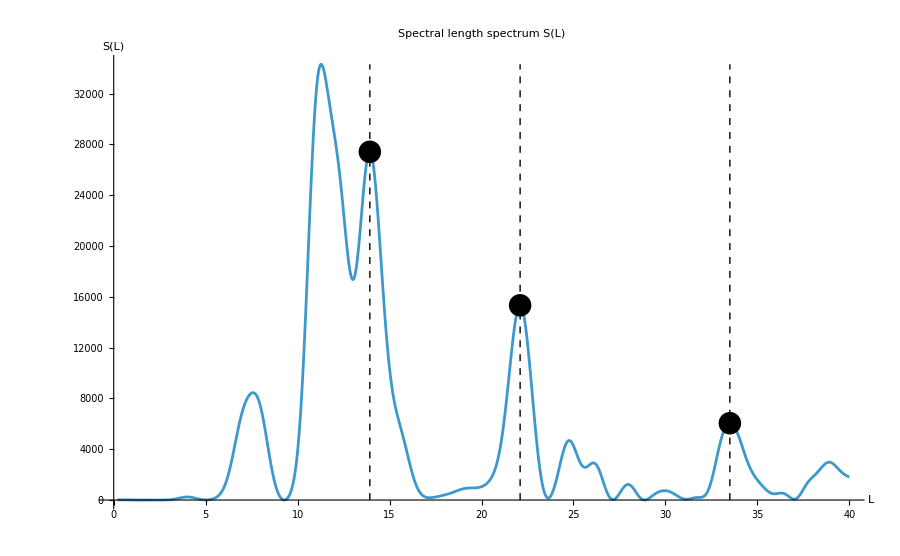

```mathematica
Clear["Global`*"];

(*-----------------------*)
(*Inputs*)
(*-----------------------*)
eigenvalueFilePath="C:\\Users\\sulta\\git\\cone-operator-lab\\data\\eigenvalues\\ellipsoid_eigs_a1_b1.5_c2.3_arnoldi-1000.txt";
eigsIndexRange={1,600};

A0fit=N@0.2371691511;
A1fit=N@(-0.5401975968);
A2fit=N@0.03937795600473376;

Lmin=0.2;Lmax=40.0;nL=12000;
wp=50;

topM=200;        (*how many peaks by height to keep*)
useMpeaks=60;    (*how many peak locations to use for triple-building*)
target=Sort[{1.0,1.5,2.3}];
radius=0.50;     (*neighborhood radius for "near target"*)

(*-----------------------*)
(*Weyl+hard volume*)
(*-----------------------*)
Vspec=6 Pi^2 A0fit;
Pspec=(3 Vspec)/(4 Pi);  (*abc*)
Print["Vspec = ",N@Vspec,"   Pspec=abc = ",N@Pspec];

Nweyl[λ_?NumericQ]:=A0fit*λ^(3/2)+A1fit*λ+A2fit*Sqrt[λ];

scaleAxesFromL[L_List]:=Module[{s},s=(Pspec/(Times@@L))^(1/3);
Sort[s L]];

(*-----------------------*)
(*Load eigenvalues*)
(*-----------------------*)
raw=Import[eigenvalueFilePath,"Table"]//Flatten;
lam=Sort[raw][[eigsIndexRange[[1]];;eigsIndexRange[[2]]]]//N;
Nvals=Length[lam];
Print["N = ",Nvals,"   λ1 = ",First[lam],"   λN = ",Last[lam]];

k=N@Range[Nvals];
F=k-(Nweyl/@lam);
t=Sqrt[lam];

(*Hann window*)
w=N@Table[0.5 (1-Cos[2 Pi (j-1)/(Nvals-1)]),{j,1,Nvals}];
Fw=F*w;
Print["Fw min/max: ",{Min[Fw],Max[Fw]}];

(*-----------------------*)
(*Length spectrum S(L)*)
(*-----------------------*)
Lgrid=Subdivide[Lmin,Lmax,nL];

Svals=Table[Abs[Total[SetPrecision[Fw,wp]*Exp[-I*SetPrecision[L,wp]*SetPrecision[t,wp]]]]^2,{L,Lgrid}]//N;

Print["S(L) min/max: ",{Min[Svals],Max[Svals]}];

(*-----------------------*)
(*Peak extraction*)
(*-----------------------*)
localMaximaIdx[y_List]:=Flatten@Position[Table[1<i<Length[y]&&y[[i]]>y[[i-1]]&&y[[i]]>y[[i+1]],{i,1,Length[y]}],True];

topPeaksFromLS[Lg_List,Sv_List,M_:200]:=Module[{idx,peaks,sorted},idx=localMaximaIdx[Sv];
peaks={Lg[[#]],Sv[[#]]}&/@idx;
sorted=Reverse@SortBy[peaks,Last];
Take[sorted,UpTo[Min[M,Length[sorted]]]]];

topPeaks=topPeaksFromLS[Lgrid,Svals,topM];
Print["#topPeaks = ",Length[topPeaks]];
Print["Top 12 peaks (L,S):"];
Print[Take[topPeaks,UpTo[12]]//TableForm];

(*-----------------------*)
(*Axis ensemble+near*)
(*-----------------------*)
Ls=topPeaks[[All,1]];
Mpeaks=Min[useMpeaks,Length[Ls]];
LsUse=Take[Ls,Mpeaks];

triples=Subsets[LsUse,{3}];
axesCand=scaleAxesFromL/@triples;

(*plausibility filter*)
axesCand=Select[axesCand,(#[[1]]>0.2&&#[[3]]<10&&#[[3]]/#[[1]]<10)&];

Print["#axes candidates = ",Length[axesCand]];

near=Select[axesCand,Norm[#-target]<=radius&];
Print["#near candidates within radius ",radius," = ",Length[near]];

If[Length[near]>0,nearSorted=SortBy[near,Norm[#-target]&];
Print["Top 30 nearest candidates (a,b,c):"];
Print[Take[nearSorted,UpTo[30]]//TableForm];];

(*-----------------------*)
(*Pick best candidate and highlight its L-peaks*)
(*-----------------------*)

If[Length[near]>0,bestAxes=First@SortBy[near,Norm[#-target]&];
Print["BEST axes = ",N@bestAxes,"   dist = ",N@Norm[bestAxes-target]];
(*Recover the L-triple(s) that produce bestAxes (within tolerance)*)tolAxes=10^-6;
axesFromTriple[L_List]:=scaleAxesFromL[L];
bestTriples=Select[triples,Norm[axesFromTriple[#]-bestAxes]<10^-8&];
bestL=If[Length[bestTriples]>0,First[bestTriples],{}];
Print["BEST L triple = ",N@bestL];,bestAxes={};
bestL={};];

(*-----------------------*)
(*Plot+highlighted peaks*)
(*-----------------------*)
basePlot=ListLinePlot[Transpose[{Lgrid,Svals}],PlotRange->All,AxesLabel->{"L","S(L)"},ImageSize->900,PlotLabel->"Spectral length spectrum S(L)"];

highlight=If[Length[bestL]==3,Show[basePlot,Graphics[{PointSize[0.018],(*points at the nearest grid values*)Table[Module[{idx=First@Ordering[Abs[Lgrid-L0],1]},{Point[{Lgrid[[idx]],Svals[[idx]]}]}],{L0,bestL}],(*vertical markers*)Table[{Dashed,Line[{{L0,0},{L0,Max[Svals]}}]},{L0,bestL}]}]],basePlot];

highlight
```